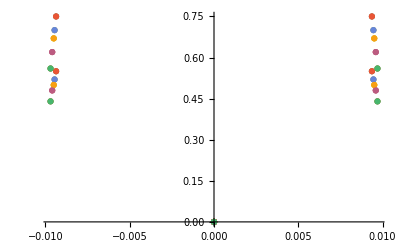

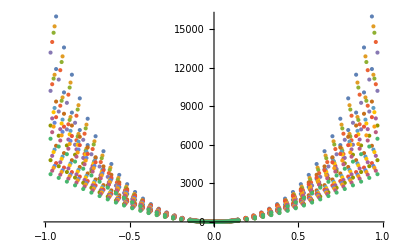

```mathematica
m={12.0107,91.224,1};kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;
(*Data in*)
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
filesC={"C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805","C_4685_760_110","C_4730_1900_110","C_4759_2500_110","C_4801_3200_110","C_4850_3805_110","C_4685_760_111","C_4730_1900_111","C_4759_2500_111","C_4801_3200_111","C_4850_3805_111"};
filesZr={"Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805","Zr_4685_760_110","Zr_4730_1900_110","Zr_4759_2500_110","Zr_4801_3200_110","Zr_4850_3805_110","Zr_4685_760_111","Zr_4730_1900_111","Zr_4759_2500_111","zr_4801_3200_111","Zr_4850_3805_111"};
filesCh={"1.harm.C_4685_760","1.harm.C_4730_1900","1.harm.C_4759_2500","1.harm.C_4801_3200","1.harm.C_4850_3805","1.harm.C_4685_760_110","1.harm.C_4730_1900_110","1.harm.C_4759_2500_110","1.harm.C_4801_3200_110","1.harm.C_4850_3805_110","1.harm.C_4685_760_111","1.harm.C_4730_1900_111","1.harm.C_4759_2500_111","1.harm.C_4801_3200_111","1.harm.C_4850_3805_111"};
filesZrh={"1.harm.Zr_4685_760","1.harm.Zr_4730_1900","1.harm.Zr_4759_2500","1.harm.Zr_4801_3200","1.harm.Zr_4850_3805","1.harm.Zr_4685_760_110","1.harm.Zr_4730_1900_110","1.harm.Zr_4759_2500_110","1.harm.Zr_4801_3200_110","1.harm.Zr_4850_3805_110","1.harm.Zr_4685_760_111","1.harm.Zr_4730_1900_111","1.harm.Zr_4759_2500_111","1.harm.Zr_4801_3200_111","1.harm.Zr_4850_3805_111"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,15}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,15}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,15}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,15}];
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,15}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,15}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,15}]
V[1,8,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15}]
V[1,10,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]

V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,15}]
V[2,4,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,15}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15}]

V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]
```

```mathematica
Clear[V[1,4,α]]
```

```mathematica
Clear[α,β,γ]
(*define 4th order potentials along 001 (alpha) 011 (beta) and 111 (gamma)*)
V[1,4,α][[1]]
V[1,4,β][[5]]
V[1,4,γ][[11]]
```

```mathematica
5774.790695038126` α^2+8775.819011023927 α^4
```

4067.37 β^2+7123.98 β^4

6383.51 γ^2-1319.62 γ^4

```mathematica
rule1={α->(x/Sqrt[1]),α->(y/Sqrt[1]),α->(z/Sqrt[1])}
rule2={β->((x+y)/Sqrt[2]),β->((x-y)/Sqrt[2]),β->((y+z)/Sqrt[2]),β->((y-z)/Sqrt[2]),β->((z+x)/Sqrt[2]),β->((z-x)/Sqrt[2])}
rule3={γ->((x+y+z)/Sqrt[3]),γ->((x+y-z)/Sqrt[3]),γ->((x-y+z)/Sqrt[3]),γ->((x-y-z)/Sqrt[3])}
```

{α→x,α→y,α→z}

{β→(x+y)/(√2),β→(x-y)/(√2),β→(y+z)/(√2),β→(y-z)/(√2),β→(x+z)/(√2),β→(-x+z)/(√2)}

{γ→(x+y+z)/(√3),γ→(x+y-z)/(√3),γ→(x-y+z)/(√3),γ→(x-y-z)/(√3)}

```mathematica
U1[e_,o_,x_,y_,z_]:=Sum[V[e,o,α][[1]]/.rule1[[i]],{i,1,3}]//Simplify
U2[e_,o_,x_,y_,z_]:=Sum[V[e,o,β][[6]]/.rule2[[i]],{i,1,6}]//Simplify
U3[e_,o_,x_,y_,z_]:=Sum[V[e,o,γ][[11]]/.rule3[[i]],{i,1,4}]//Simplify
UUU[e_,o_,x_,y_,z_]:=U1[e,o,x,y,z]+(U2[e,o,x,y,z]-U1[e,o,x,y,z])+(U3[e,o,x,y,z]-U2[e,o,x,y,z]-U1[e,o,x,y,z])
```

```mathematica
V[1,2,x][[1]]
Sum[V[1,2,α][[1]]/.rule1[[i]],{i,1,3}]/.{y->0,z->0}
With[{y=0,z=0},Sum[V[1,2,α][[1]]/.rule1[[i]],{i,1,3}]-Sum[V[1,2,β][[6]]/.rule2[[i]],{i,1,6}]]
UUU[1,2,x,y,z]/.{y->0,z->0}//Expand
```

6264.46 x^2

0.+6264.46 x^2

6264.46 x^2-3132.23 (x-y)^2+6264.46 y^2-3132.23 (x+y)^2-3132.23 (y-z)^2+6264.46 z^2-3132.23 (-x+z)^2-3132.23 (x+z)^2-3132.23 (y+z)^2

0.+2088.15 x^2

```mathematica
V[1,2,α][[1]]
U3[1,2,x,y,z]
UUU
```

6264.46 α^2

0.+8352.61 x^2+8352.61 y^2+8352.61 z^2

UUU

```mathematica
V[1,2,x][[1]]
```

6264.46 x^2

```mathematica
(*C harmonic*)
UUU[1,2,x,y,z]//Expand
(*Zr 12th order anharmonic*)
UUU[1,4,x,y,z]/.{y->0,z->0}//Expand
```

0.+2088.15 x^2+2088.15 y^2+2088.15 z^2

0.+2736.56 x^2-9362.32 x^4

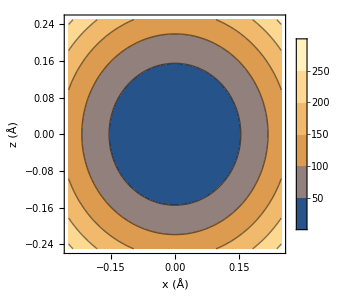
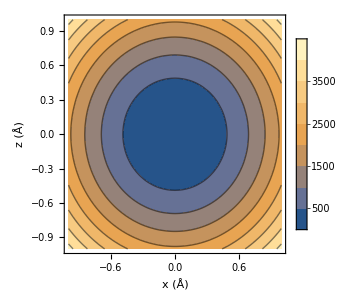

```mathematica
cHar
```

```mathematica
contourOptions={AxesLabel->{"x (Å)","z (Å)"},ImageSize->300};
```

```mathematica
cHar=Table[With[{B=0.25*i},ContourPlot[UUU[1,2,x,y,z]/.y->0,{x,-B,B},{z,-B,B},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,4,3}];
cAnh=Table[With[{B=0.25*i},ContourPlot[UUU[1,6,x,y,z]/.y->0,{x,-B,B},{z,-B,B},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,4,3}];
zHar=Table[With[{B=0.25*i},ContourPlot[UUU[2,2,x,y,z]/.y->0,{x,-B,B},{z,-B,B},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,4,3}];
```

```mathematica
zAnh=Table[With[{B=0.25*i},ContourPlot[UUU[2,6,x,y,z]/.y->0,{x,-B,B},{z,-B,B},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,4,3}];
```

$Aborted

```mathematica
(*Carbon harmonic and anharmonic*)
GraphicsGrid[{{cHar[[1]],cHar[[2]]},{cAnh[[1]],cAnh[[2]]}},ImageSize->1000]
(*Zr harmonic and anharmonic*)
GraphicsGrid[{{zHar[[1]],zHar[[2]]},{zAnh[[1]],zAnh[[2]]}}]
```

-Graphics-

-Graphics-

```mathematica
ContourPlot3D[UUU[1,6,x,y,z],{x,-B,B},{y,-B,B},{z,-B,B}]
```

-Graphics3D-

```mathematica
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=Table[V[1,2,x][[i]][[1]],{i,1,5}]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=Table[V[2,2,x][[i]][[1]],{i,1,5}]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{6264.46,5810.6,5528.52,5208.33,4676.37}

cOmega0 in meV/Ang**2/AMU is approximately

{32.2978,31.1058,30.3414,29.4497,27.9052}

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{8542.44,7821.96,7408.22,6727.43,5951.75}

Z_Omega_0 in meV/Ang**2/AMU is approximately

{13.6852,13.0954,12.7443,12.1447,11.4231}

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=70;
(*Define bounds for plotting and solving eigenproblem*)
B=1;H=2000;
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒharc=-(1/(2m[[1]]))*u''[x,y,z]+UUU[1,2,x,y,z]*u[x,y,z]
ℒanhc=-(1/(2m[[1]]))*u''[x,y,z]+UUU[1,4,x,y,z]*u[x,y,z]
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}},"Eigensystem"->{"Arnoldi"}}};
(*,MaxIterations->Infinity*)
```

(0.+23969.8 x^2+23969.8 y^2+23969.8 z^2) u[x,y,z]-0.0416295 u''[x,y,z]

(0.+5774.79 x^2+15313.3 x^4+5774.79 y^2+15313.3 y^4+22420.9 z^2+15313.3 z^4+y^2 (8511.35-3518.98 z^2)+x^2 (8511.35-3518.98 y^2-3518.98 z^2)+y^2 (8134.74+21371.9 z^2)+x^2 (8134.74+21371.9 y^2+21371.9 z^2)) u[x,y,z]-0.0416295 u''[x,y,z]

```mathematica
test=NDEigensystem[(23969.8162333987 x^2+23969.8162333987 y^2+23969.8162333987 z^2)*u[x,y,z]-0.041629546987269686*Laplacian[u[x,y,z],{x,y,z}],u[x,y,z],{x,-B/5,B/5},{y,-B/5,B/5},{z,-B/5,B/5},Neigenvalues,Evaluate@solverOptions]//Timing;
```

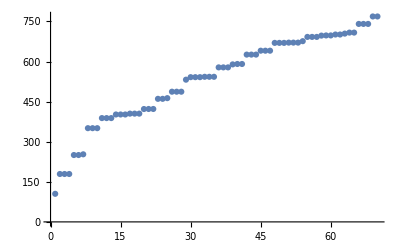

```mathematica
ListPlot@test[[2]][[1]]
```

```mathematica
ContourPlot3D[test[[2]][[2]][[1]]/.{x->x,y->y,z->z},{x,-B/5,B/5},{y,-B/5,B/5},{z,-B/5,B/5}]
```

-Graphics3D-

```mathematica
test={105.11086732920613,179.29736590887987,250.4118816254245}
test[[3]]/test[[2]]
```

{105.111,179.297,250.412}

1.39663

```mathematica
eigensysCanh=NDEigensystem[ℒanhc,u[x,y,z],{{x,-B,B},{y,-B,B},{z,-B,B}},Neigenvalues,Evaluate@solverOptions]
```

```mathematica
Transformation to polar field
SUUU[R,θ,ϕ]=TransformedField["Cartesian"->"Spherical",UUU[x,y,z],{x,y,z}->{R,θ,ϕ}]
```

-2639.23 (-7.2561 R^2 Cos[θ]^2+1. R^4 Cos[θ]^4-7.2561 R^2 Cos[ϕ]^2 Sin[θ]^2+1. R^4 Cos[ϕ]^4 Sin[θ]^4-12.0935 R^2 Sin[θ]^2 Sin[ϕ]^2+3. R^4 Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2+3. R^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2+1.5 R^4 Sin[θ]^4 Sin[ϕ]^4)

```mathematica
SUUU/.R->1
```

-2639.23 (-7.2561 Cos[θ]^2+1. Cos[θ]^4-7.2561 Cos[ϕ]^2 Sin[θ]^2+1. Cos[ϕ]^4 Sin[θ]^4-12.0935 Sin[θ]^2 Sin[ϕ]^2+3. Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2+3. Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2+1.5 Sin[θ]^4 Sin[ϕ]^4)

```mathematica
SphericalPlot3D[SUUU/.R->1,{θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-